# MATH 340: 9/18/19 Worksheet Solns

## Part 1: Generating analytical solutions and plotting them

### Question a:

```mathematica
solna=DSolve[{y'[x]==3(y[x]+7)x^2,y[0]==2},y[x],x]
```

{{y[x]→-7+9 ⅇ^(x^3)}}

```mathematica
Plot[y[x]/.solna,{x,0,5}]
```

-Graphics-

### Question b:

```mathematica
(* NOTE: Dr. McNelis had a type-o (so sorry!!) and the second term on the Left Hand Side of the equation was to be 3*x^3*y rather *)
```

```mathematica
solnb=DSolve[{(x^2+1)*y'[x]+3*x^3*y[x]==6*x*Exp[(-3/2)*(x^2)],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-(3 x^2)/2) (-2+3 √(1+x^2)+3 x^2 √(1+x^2))}}

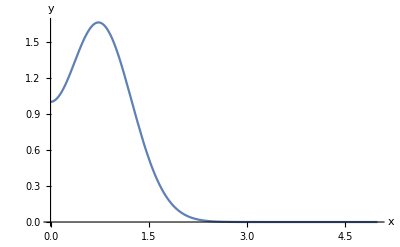

```mathematica
Plot[y[x]/.solnb, {x,0,5},AxesLabel->{x,y}]
```

### Question c:

```mathematica
(* This equation needs TWO initial conditions to evaluate without having an arbitrary constant in the solution. Make up your own initial condition for x'. *)
```

```mathematica
solnc=DSolve[{x''[t]-x'[t]+4x[t]==0,x[0]==1,x'[0]==1},x[t],t]
```

{{x[t]→1/15 ⅇ^(t/2) (15 Cos[(√15 t)/2]+√15 Sin[(√15 t)/2])}}

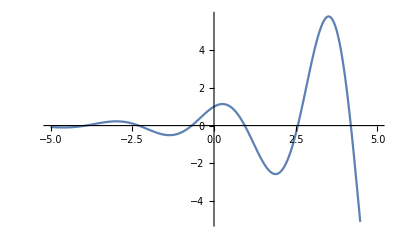

```mathematica
Plot[x[t]/.solnc,{t,-5,5}]
```

```mathematica
(*  Just for fun, to build on this ... we can use Manipulate to see what happens as we change our initial slope.  See what happens to the solution as we adjust that value.  Fun!! *)
```

```mathematica
Manipulate[solnManip=DSolve[{x''[t]-x'[t]+4x[t]==0,x[0]==1,x'[0]==k},x[t],t];Plot[x[t]/.solnManip,{t,-5,5},PlotRange->{-10,10}],{k,-3,5}]
```

### Question d:

```mathematica
solnd=DSolve[{x'[t]==5x[t]-17y[t],y'[t]==8x[t]-7y[t],x[0]==4,y[0]==2},{x[t],y[t]},t]
```

{{x[t]→-ⅇ^-t (-4 Cos[10 t]+Sin[10 t]),y[t]→2 ⅇ^-t (Cos[10 t]+Sin[10 t])}}

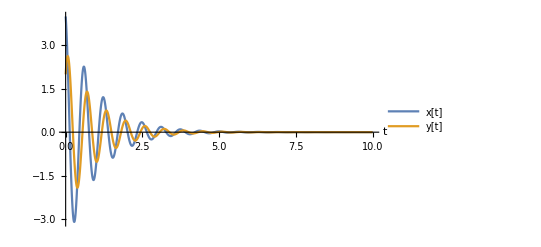

```mathematica
(* First we can plot both functions over time.  Note, to get them to show up in different colors, and thus have the legend work, we type {x[t]/.solnd,y[t]/.solnd} rather than {x[t],y[t]}/.solnd *)
Plot[{x[t]/.solnd,y[t]/.solnd}, {t,0,10},PlotRange->All,AxesLabel -> Automatic,PlotLegends->{"x[t]","y[t]"}]
```

```mathematica
(*  Now we can see what happens if we plot our (x(t),y(t)) values in a parametric plot *)
```

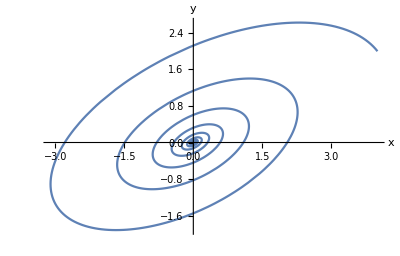

```mathematica
ParametricPlot[{x[t],y[t]}/.solnd,{t,0,10},PlotRange->Full,AxesLabel->{x,y}]
```

## Part 2: Numerical solutions

### Question a:

```mathematica
s2a=NDSolve[{y'[x]==x+CubeRoot[y[x]],y[0]==-1},y[x],{x,0,2}]
```

{{y[x]→InterpolatingFunction[{{0., 2.}}, <>][x]}}

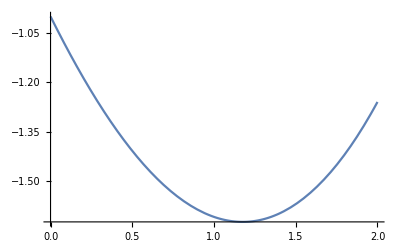

```mathematica
Plot[Evaluate[y[x]/.s2a],{x,0,2},PlotRange->All]
```

### Question b:

```mathematica
s2b=NDSolve[{x'[t]==0.2x[t]-0.005x[t]*y[t],y'[t]==-0.5y[t]+0.01x[t]*y[t],x[0]==70,y[0]==30},{x[t],y[t]},{t,0,80}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

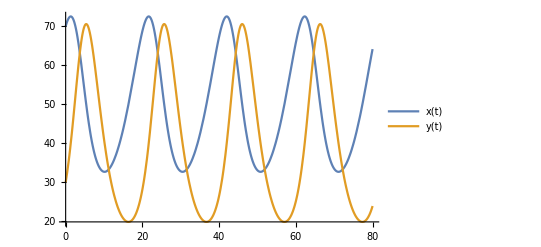

```mathematica
Plot[{x[t]/.s2b,y[t]/.s2b},{t,0,80},PlotLegends->{"x(t)","y(t)"}]
```

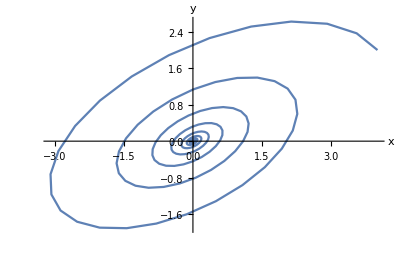

```mathematica
ParametricPlot[{x[t],y[t]}/.solnd,{t,0,80},PlotRange->Full,AxesLabel->{x,y}]
```